```mathematica
Clear[a, b, c, d, f]
```

```mathematica
(* Logistic 5 Param equation #8 for Mar8,returns dose concentration given instrument response.  Asymptotes are 'a' on the left, and 'd' on the right. *)
```

```mathematica
logistic5p[r_]:= (a-d)/(1+(r/c)^b)^f+d
```

```mathematica
(* Invert the equation to obtain instrument response as a function of dose concentration. *)
```

```mathematica
Solve[t==logistic5p[r], r]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→c (-1+((-a+d)/(d-t))^(1/f))^(1/b)}}

```mathematica
(* Set second derivative to zero to obtain dose concentration value for which instrument response is at its midpoint. *)
```

```mathematica
Simplify[logistic5p''[r]==0]
```

(b (a-d) f (r/c)^b (1+(r/c)^b)^(-1-f) (1+(r/c)^b+b (-1+f (r/c)^b)))/r==0

```mathematica
Solve[1+(r/c)^b+b (-1+f (r/c)^b)==0, r]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→c ((-1+b)/(1+b f))^(1/b)}}

```mathematica
(* Example curve using coefficients obtained in the Excel Solver. *)
```

```mathematica
a=0;b=2.58; c=0.82; d=1.125; f=2.5
```

2.5

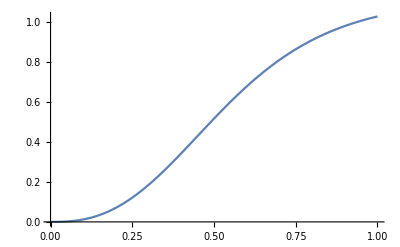

```mathematica
Plot[logistic5p[r],  {r, 0, 1}]
```